```mathematica
SetDirectory[NotebookDirectory[]];
```

Fig1a_localized_heterogeneity.png

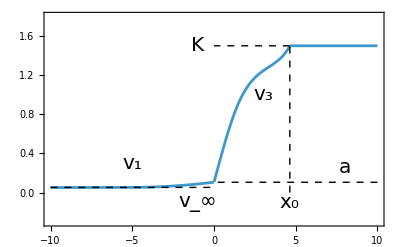

Fig1a_localized_heterogeneity.png

```mathematica
(*Case 1: Barrier for the dirac delta case*)
filename="Fig1a_localized_heterogeneity.png"
(*Must satisfy αγ>1*)
γ=4;α=0.4;K=1.5;

sg1=1;
sg2=1;
sg3=1;
L=0;
f[v_]=v(1-v)(v-α);
h[v_]=Min[f[-v],-f[v]];

g[v_]=-(v-v^2);
g2[v_]=Min[-g[v],g[-v]];

eqn=FindRoot[h[v]-v/γ==0,{v,0.2}];
eqn2=FindRoot[h[v]-v/γ==0,{v,1.3}];
a1=v/.eqn;
b=v/.eqn2;

(*Step 1: the approach*)
a=0.9Min[1,a1];
vinf=a/2; (*This requires h[v]-v/γ>0 between vinf and a*)

(*g1a=Plot[{h[v]-v/γ},{v,0,1.5},PlotRange->{-0.4,0.5},Frame->True];
g2a=Graphics[{Dashed,Line[{{a,0},{a,2}}]}];
g3a=Graphics[{Dashed,Line[{{vinf,0},{vinf,2}}]}];
Show[g1a,g2a,g3a]*)

V1=NDSolveValue[{sg1 v''[x]==Which[v[x]>vinf+10^(-5),h[v[x]]-v[x]/γ,True,0],
v[0]==a, v'[0]==Sqrt[2]Sqrt[(1/sg1)Integrate[h[u]-u/γ,{u,vinf,a}]]}
,v,{x,-10,0}];

(*Compute p* *)
(*Step 2: The climb*)
Dv1[p_]=0;
Dv2[p_]=p g2[a];
eqnp=FindRoot[ V1'[0]Dv2[p]+0.5 Dv2[p]^2+Integrate[h[v]-v/γ,{v,a+Dv1[p],b}],{p,0.2}];
p1=p+0.1/.eqnp;
(*Step 3: The Summit*)
V3=NDSolveValue[{sg3 v''[x]==h[v[x]]-v[x]/γ,v[0]==V1[0]+Dv1[p1],v'[0]==V1'[0]+Dv2[p1]},v,{x,0,6}];
(*Together*)
eqnx0=FindRoot[V3[x]==K,{x,4}];
x0=x/.eqnx0;
VV[x_]=Which[x<0,V1[x],x<x0,V3[x],True,K];
g1=Plot[VV[x],{x,-10,10},Frame->True,PlotRange->{-0.3,1.8}];
lineK=Graphics[{Dashed,Line[{{x0,K},{0,K}}]}];
linex0=Graphics[{Dashed,Line[{{x0,0},{x0,K}}]}];
labelK=Graphics[Text[Style["K",FontSize->20],{-1,K},{0,0}]];
labelx0=Graphics[Text[Style["x_0",FontSize->20],{x0,-0.1},{0,0}]];
linea=Graphics[{Dashed,Line[{{10,a},{0,a}}]}];
labela=Graphics[Text[Style["a",FontSize->20],{8,a+0.15},{0,0}]];
linevinf=Graphics[{Dashed,Line[{{-10,vinf},{0,vinf}}]}];
labelvfinf=Graphics[Text[Style["v_∞",FontSize->20],{-1,vinf-0.15},{0,0}]];
labelv1v2=Graphics[{Text[Style["v_1",FontSize->20],{-5,0.3},{0,0}],
Text[Style["v_3",FontSize->20],{3,1},{0,0}]}];
img=Show[g1,lineK,labelK,linex0,labelx0,linea,labela,labelv1v2,linevinf,labelvfinf]
Export[filename,img]
```

Fig1b_localized_heterogeneity.png

0.023381

Speed Required = 0.690533

874.809

Paramater p required= 874.809

L= 0.0705751

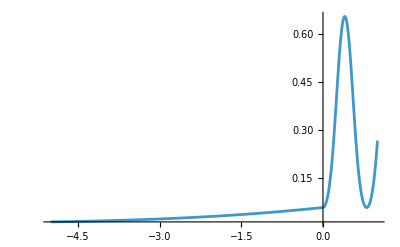

v2[0]=0.0584524; v2'[0]=0.0176896

v3[L]=0.0818334; v3'[l]=0.672366

NDSolveValue::ndsz: At x == 4.87591, step size is effectively zero; singularity or stiff system suspected.

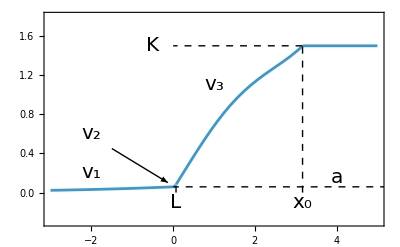

Fig1b_localized_heterogeneity.png

```mathematica
(*Case 2: Additive heterogeneity, distributed over an interval*)
filename="Fig1b_localized_heterogeneity.png"
γ=4;α=0.4;K=1.5;
sg1=1;sg2=1;sg3=1;

f[v_]=v(1-v)(v-α);
h[v_]=Min[f[-v],-f[v]];
g[v_]=f[v];
g2[v_]=Min[-g[v],g[-v]];

eqn=FindRoot[h[v]-v/γ==0,{v,0.2}];
eqn2=FindRoot[h[v]-v/γ==0,{v,1.3}];
a1=v/.eqn;
b=v/.eqn2;

(*Step 1: the approach. The interval [a00,a01] is where the hetogeneity will act*)
a=0.5Min[1,a1];
a01=0.7Min[1,a1]; (*a+δ*)
δ=a01-a;
vinf=0.2a;

(*g1a=Plot[{h[v]-v/γ},{v,0,1.5},PlotRange->{-0.4,0.5},Frame->True];
g2a=Graphics[{Dashed,Line[{{a,0},{a,2}}]}];
g3a=Graphics[{Dashed,Line[{{vinf,0},{vinf,2}}]}];
Show[g1a,g2a,g3a]*)

V1=NDSolveValue[{sg1 v''[x]==Which[v[x]>vinf+10^(-5),h[v[x]]-v[x]/γ,True,0],
v[0]==a, v'[0]==Sqrt[2]Sqrt[(1/sg1)Integrate[h[u]-u/γ,{u,vinf,a}]]},
v,{x,-10,0}];

(*Step 2: The climb*)
(*Increase on the slope required for crossing*)
eqnp=FindRoot[0.5vel0^2 + V1'[0]vel0+0.5 V1'[0]^2+Integrate[h[v]-v/γ,{v,a01 ,b}],{vel0,2}];
vel=vel0+0.02/.eqnp;
Print["Speed Required = ",vel0]
eqnp1=FindRoot[(h[a01]-a01/γ+p h[a01])/(V1'[0]+vel)==vel/δ,{p,1}];
p1=p/.eqnp1
Print["Paramater p required= ",p1]
p1=450;



V2=NDSolveValue[{sg2 v''[x]==(1+p1)h[v[x]]-v[x]/γ,v[0]==V1[0],v'[0]==V1'[0]},v,{x,0,3}];
eqn3=FindRoot[V2[x]==a01,{x,0}];
L=x/.eqn3;
Print["L= ",L]
VV1[x_]=Which[x<0,V1[x],x<1,V2[x]];
Plot[VV1[x],{x,-5,1},PlotRange->All]


(*eqnp=FindRoot[Dv2[p]^2 + V1'[-L]Dv2[p]+0.5 V1'[-L]^2+Integrate[h[v]-v/γ,{v,a +2p V1[-L] ,1.2831}],{p,2}];*)
(*p1=p+0.1/.eqnp;*)
(*Step 3: The Summit*)
V1=NDSolveValue[{sg1 v''[x]==Which[v[x]>vinf+10^(-5),h[v[x]]-v[x]/γ,True,0],v[0]==a, v'[0]==Sqrt[2]Sqrt[(1/sg1)Integrate[h[u]-u/γ,{u,vinf,a}]]},v,{x,-10,0}];
V2=NDSolveValue[{sg2 v''[x]==(1+p1)h[v[x]]-v[x]/γ,v[0]==V1[0],v'[0]==V1'[0]},v,{x,0,L}];
Print["v2[0]=",V2[0],"; v2'[0]=",V2'[0]]
Print["v3[L]=",V2[L],"; v3'[l]=",V2'[L]]
V3=NDSolveValue[{sg3 v''[x]==h[v[x]]-v[x]/γ,v[L]==V2[L],v'[L]==V2'[L]},v,{x,L,L+10}];
(*Together*)
eqnx0=FindRoot[V3[x]==K,{x,L+2}];
x0=x/.eqnx0;

VV[x_]=Which[x<0,V1[x],x<L,V2[x],x<x0,V3[x],True,K];
g1=Plot[VV[x],{x,-3,5},Frame->True,PlotRange->{-0.3,1.8}];
lineK=Graphics[{Dashed,Line[{{x0,K},{0,K}}]}];
linex0=Graphics[{Dashed,Line[{{x0,0},{x0,K}}]}];
labelK=Graphics[Text[Style["K",FontSize->20],{-0.5,K},{0,0}]];
labelx0=Graphics[Text[Style["x_0",FontSize->20],{x0,-0.1},{0,0}]];
linea=Graphics[{Dashed,Line[{{10,a},{0,a}}]}];
labela=Graphics[Text[Style["a",FontSize->20],{4,a+0.1},{0,0}]];
labelv1v2=Graphics[{Text[Style["v_1",FontSize->20],{-2,0.2},{0,0}],
Text[Style["v_2",FontSize->20],{-2,0.6},{0,0}],
Text[Style["v_3",FontSize->20],{1,1.1},{0,0}]}];
arrowv2=Graphics[Arrow[{{-1.5,0.45},{L-0.2,a01+0.02}}]];
lineL1=Graphics[{Dashed,Line[{{L,0},{L,V2[0]}}]}];
labelL1=Graphics[Text[Style["L",FontSize->20],{L,-0.1},{0,0}]];
lineL2=Graphics[{Dashed,Line[{{L,0},{L,V2[L]}}]}];
labelL2=Graphics[Text[Style["L",FontSize->20],{L,-0.1},{0,0}]];
linevinf=Graphics[{Dashed,Line[{{-10,vinf},{0,vinf}}]}];
labelvfinf=Graphics[Text[Style["v_∞",FontSize->20],{-1,vinf-0.15},{0,0}]];

img=Show[g1,lineK,labelK,linex0,labelx0,linea,labela,labelv1v2,lineL1,labelL1,arrowv2]
Export[filename,img]
```

Fig1c_localized_heterogeneity.png

{v→0.232769}

{v→1.21723}

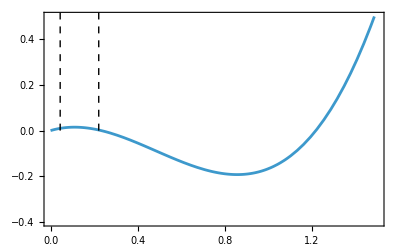

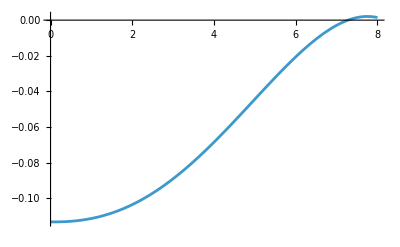

0.000163378

NDSolveValue::ndsz: At x == 13.9455, step size is effectively zero; singularity or stiff system suspected.

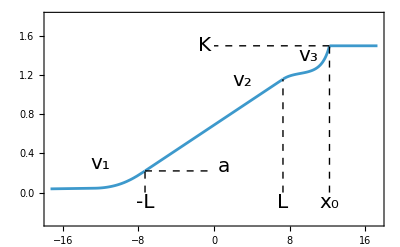

Fig1c_localized_heterogeneity.png

```mathematica
(*Case 3: Segment with depressed dynamics*)
filename="Fig1c_localized_heterogeneity.png"
γ=6;α=0.45;K=1.5;xmin=-50;xmax=50;maxtime=5;ep=0.08;
sg1=1;
sg2=1;
sg3=1;
L=0;
f[v_]=v(1-v)(v-α);
h[v_]=Min[f[-v],-f[v]];
a0=1;
(*h is positive for *)
eqn=FindRoot[h[v]-v/γ==0,{v,0.2}]
eqn2=FindRoot[h[v]-v/γ==0,{v,1.3}]
a1=v/.eqn;

(*Step 1: the approach*)
a=0.95Min[1,a1];
vinf=0.2a;
g1a=Plot[{h[v]-v/γ},{v,0,1.5},PlotRange->{-0.4,0.5},Frame->True];
g2a=Graphics[{Dashed,Line[{{a,0},{a,2}}]}];
g3a=Graphics[{Dashed,Line[{{vinf,0},{vinf,2}}]}];
(*Show[g1a,g2a,g3a]*)

V1=NDSolveValue[{sg1 v''[x]==Which[v[x]>vinf+10^(-5),h[v[x]]-v[x]/γ,True,0],v[-L]==a, v'[-L]==Sqrt[2]Sqrt[(1/sg1)Integrate[h[u]-u/γ,{u,vinf,a}]]},v,{x,-10,-L}];
(*Compute p* *)
(*Step 2: The climb*)
Dv1[p_]=2p V1'[-L];
Dv2[p_]=0;
(*Plot[0.5 Dv2[p]^2 + V1'[-L]Dv2[p]+0.5 V1'[-L]^2+Integrate[h[v]-v/γ,{v,a +2p V1'[-L] ,1.21723}],{p,0,8}]*)
p1=7.3;
0.5Dv2[p1]^2 + V1'[-L]Dv2[p1]+0.5 V1'[-L]^2+Integrate[h[v]-v/γ,{v,a +2*p1* V1'[-L] ,1.21723}]

(*eqnp=FindRoot[Dv2[p]^2 + V1'[-L]Dv2[p]+0.5 V1'[-L]^2+Integrate[h[v]-v/γ,{v,a +2p V1[-L] ,1.2831}],{p,2}];*)
(*p1=p+0.1/.eqnp;*)
L=p1;
(*Step 3: The Summit*)
V1=NDSolveValue[{sg1 v''[x]==Which[v[x]>vinf+10^(-4),h[v[x]]-v[x]/γ,True,0],v[-L]==a, v'[-L]==Sqrt[2]Sqrt[(1/sg1)Integrate[h[u]-u/γ,{u,vinf,a}]]},v,{x,-L-10,-L}];
V2=NDSolveValue[{sg2 v''[x]==0,v[-L]==V1[-L], v'[-L]==V1'[-L]},v,{x,-L,L}];
V3=NDSolveValue[{sg3 v''[x]==h[v[x]]-v[x]/γ,v[L]==V2[L],v'[L]==V2'[L]},v,{x,L,L+10}];
(*Together*)
eqnx0=FindRoot[V3[x]==K,{x,L+5}];
x0=x/.eqnx0;
VV[x_]=Which[x<-L,V1[x],x<L,V2[x],x<x0,V3[x],True,K];
g1=Plot[VV[x],{x,-L-10,L+10},Frame->True,PlotRange->{-0.3,1.8}];
lineK=Graphics[{Dashed,Line[{{x0,K},{0,K}}]}];
linex0=Graphics[{Dashed,Line[{{x0,0},{x0,K}}]}];
labelK=Graphics[Text[Style["K",FontSize->20],{-1,K},{0,0}]];
labelx0=Graphics[Text[Style["x_0",FontSize->20],{x0,-0.1},{0,0}]];
linea=Graphics[{Dashed,Line[{{-L,a},{0,a}}]}];
labela=Graphics[Text[Style["a",FontSize->20],{1,a+0.05},{0,0}]];
labelv1v2=Graphics[{Text[Style["v_1",FontSize->20],{-12,0.3},{0,0}],
Text[Style["v_2",FontSize->20],{3,1.15},{0,0}],
Text[Style["v_3",FontSize->20],{10,1.4},{0,0}]}];
lineL1=Graphics[{Dashed,Line[{{-L,0},{-L,a}}]}];
labelL1=Graphics[Text[Style["-L",FontSize->20],{-L,-0.1},{0,0}]];
lineL2=Graphics[{Dashed,Line[{{L,0},{L,V2[L]}}]}];
labelL2=Graphics[Text[Style["L",FontSize->20],{L,-0.1},{0,0}]];

img=Show[g1,lineK,labelK,linex0,labelx0,linea,labela,labelv1v2,lineL1,lineL2,labelL1,labelL2]
Export[filename,img]
```

Fig1d_localized_heterogeneity.png

{v→0.116905}

{v→1.2831}

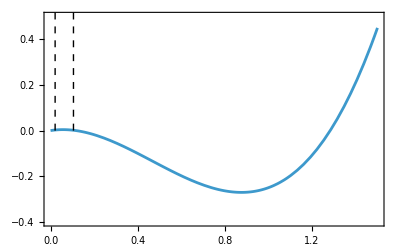

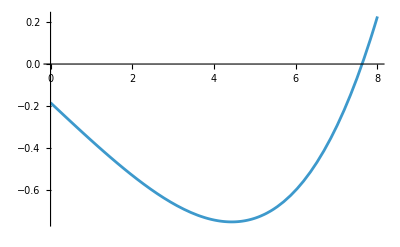

0.0427321

1.81795

-1.60973

NDSolveValue::ndsz: At x == 2.23529, step size is effectively zero; singularity or stiff system suspected.

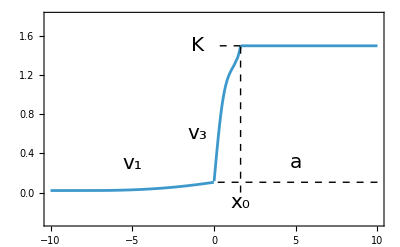

Fig1d_localized_heterogeneity.png

```mathematica
(*Case 4: Heterogeneity in the conductivity*)
filename="Fig1d_localized_heterogeneity.png"
γ=4;α=0.4;K=1.5;xmin=-50;xmax=50;maxtime=5;ep=0.08;
sg1=1;
L=0;

f[v_]=v(1-v)(v-α);
h[v_]=Min[f[-v],-f[v]];
a0=1;
(*h is positive for *)
eqn=FindRoot[h[v]-v/γ==0,{v,0.2}]
eqn2=FindRoot[h[v]-v/γ==0,{v,1.3}]
a1=v/.eqn;

(*Step 1: the approach*)
a=0.9Min[1,a1];
vinf=0.2a;
g1a=Plot[{h[v]-v/γ},{v,0,1.5},PlotRange->{-0.4,0.5},Frame->True];
g2a=Graphics[{Dashed,Line[{{a,0},{a,2}}]}];
g3a=Graphics[{Dashed,Line[{{vinf,0},{vinf,2}}]}];
(*Show[g1a,g2a,g3a]*)

V1=NDSolveValue[{sg1 v''[x]==Which[v[x]>vinf+10^(-5),h[v[x]]-v[x]/γ,True,0],v[-L]==a, v'[-L]==Sqrt[2]Sqrt[(1/sg1)Integrate[h[u]-u/γ,{u,vinf,a}]]},v,{x,-10,-L}];
(*Compute p* *)
(*Step 2: The climb*)
Dv1[p_]=0;
Dv2[p_]=((1+p)^2-1)V1'[-L];
(*Plot[0.5Dv2[p]^2 + V1'[-L]Dv2[p]+0.5 V1'[-L]^2+(1+p) Integrate[h[v]-v/γ,{v,a +Dv1[p] ,1.2831}],{p,0,8}]*)
p1=7.7;
0.5Dv2[p1]^2 + V1'[-L]Dv2[p1]+0.5 V1'[-L]^2+(1+p1) Integrate[h[v]-v/γ,{v,a +Dv1[p1] ,1.2831}]

(*eqnp=FindRoot[Dv2[p]^2 + V1'[-L]Dv2[p]+0.5 V1'[-L]^2+Integrate[h[v]-v/γ,{v,a +2p V1[-L] ,1.2831}],{p,2}];*)
(*p1=p+0.1/.eqnp;*)
(*Step 3: The Summit*)
sg1=1;
sg3=1/(1+p1);
V1=NDSolveValue[{sg1 v''[x]==Which[v[x]>vinf+10^(-5),h[v[x]]-v[x]/γ,True,0],v[-L]==a, v'[-L]==Sqrt[2]Sqrt[(1/sg1)Integrate[h[u]-u/γ,{u,vinf,a}]]},v,{x,-L-10,-L}];
V1'[-L]+Dv2[p1]
(1+p1) Integrate[h[v]-v/γ,{v,a +Dv1[p1] ,1.2831}]
V3=NDSolveValue[{sg3 v''[x]==h[v[x]]-v[x]/γ,v[L]==V1[-L]+Dv1[p1],v'[L]==V1'[-L]+Dv2[p1]},v,{x,L,L+10}];
(*Together*)
eqnx0=FindRoot[V3[x]==K,{x,L+2}];
x0=x/.eqnx0;

VV[x_]=Which[x<-L,V1[x],x<L,V2[x],x<x0,V3[x],True,K];
g1=Plot[VV[x],{x,-L-10,L+10},Frame->True,PlotRange->{-0.3,1.8}];
lineK=Graphics[{Dashed,Line[{{x0,K},{0,K}}]}];
linex0=Graphics[{Dashed,Line[{{x0,0},{x0,K}}]}];
labelK=Graphics[Text[Style["K",FontSize->20],{-1,K},{0,0}]];
labelx0=Graphics[Text[Style["x_0",FontSize->20],{x0,-0.1},{0,0}]];
linea=Graphics[{Dashed,Line[{{10,a},{0,a}}]}];
labela=Graphics[Text[Style["a",FontSize->20],{5,a+0.2},{0,0}]];
labelv1v2=Graphics[{Text[Style["v_1",FontSize->20],{-5,0.3},{0,0}],
Text[Style["v_3",FontSize->20],{-1,0.6},{0,0}]}];
lineL1=Graphics[{Dashed,Line[{{-L,0},{-L,a}}]}];
labelL1=Graphics[Text[Style["-L",FontSize->20],{-L,-0.1},{0,0}]];
lineL2=Graphics[{Dashed,Line[{{L,0},{L,V2[L]}}]}];
labelL2=Graphics[Text[Style["L",FontSize->20],{L,-0.1},{0,0}]];

img=Show[g1,lineK,labelK,linex0,labelx0,linea,labela,labelv1v2]
Export[filename,img]
```

Fig1e_localized_heterogeneity.png

-Graphics-

NDSolveValue::ndsz: At x == 1.59152, step size is effectively zero; singularity or stiff system suspected.

{x→0.812418}

NDSolveValue::ndsz: At x == 1.40785, step size is effectively zero; singularity or stiff system suspected.

NDSolveValue::ndsz: At x == 3.4289, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {-10.812} lies outside the range of data in the interpolating function. Extrapolation will be used.

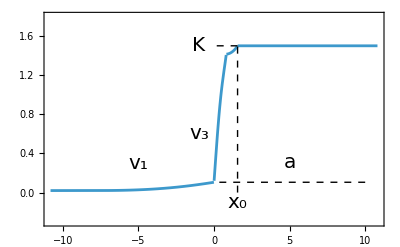

Fig1e_localized_heterogeneity.png

```mathematica
(*Case 5: Heterogeneity in the conductivity, two switches*)
filename="Fig1e_localized_heterogeneity.png"
γ=4;α=0.4;K=1.5;xmin=-50;xmax=50;maxtime=5;ep=0.08;
p1=9;
sg1=1;
sg2=1/(1+p1);
sg3=1;

f[v_]=v(1-v)(v-α);
h[v_]=Min[f[-v],-f[v]];
a0=1;
(*h is positive for *)
eqn=FindRoot[h[v]-v/γ==0,{v,0.2}];
eqn2=FindRoot[h[v]-v/γ==0,{v,1.3}];
a1=v/.eqn;
u0=v/.eqn2;

(*Step 1: the approach*)
a=0.9Min[1,a1];
vinf=0.2a;
g1a=Plot[{h[v]-v/γ},{v,0,1.5},PlotRange->{-0.4,0.5},Frame->True];
g2a=Graphics[{Dashed,Line[{{a,0},{a,2}}]}];
g3a=Graphics[{Dashed,Line[{{vinf,0},{vinf,2}}]}];
Show[g1a,g2a,g3a]

V1=NDSolveValue[{sg1 v''[x]==Which[v[x]>vinf+10^(-5),h[v[x]]-v[x]/γ,True,0],v[0]==a, v'[0]==Sqrt[2]Sqrt[(1/sg1)Integrate[h[u]-u/γ,{u,vinf,a}]]},v,{x,-10,0}];
(*Compute p* *)
(*Step 2: The climb*)

V2=NDSolveValue[{sg2 v''[x]==h[v[x]]-v[x]/γ,v[0]==V1[-L],v'[0]==(sg1^2/sg2^2)V1'[-L]},v,{x,0,10}];
eqn3=FindRoot[V2[x]==u0,{x,1}]
L=x/.eqn3;

(*eqnp=FindRoot[Dv2[p]^2 + V1'[-L]Dv2[p]+0.5 V1'[-L]^2+Integrate[h[v]-v/γ,{v,a +2p V1[-L] ,1.2831}],{p,2}];*)
(*p1=p+0.1/.eqnp;*)
(*Step 3: The Summit*)
V1=NDSolveValue[{sg1 v''[x]==Which[v[x]>vinf+10^(-5),h[v[x]]-v[x]/γ,True,0],v[0]==a, v'[0]==Sqrt[2]Sqrt[(1/sg1)Integrate[h[u]-u/γ,{u,vinf,a}]]},v,{x,-10,0}];
V2=NDSolveValue[{sg2 v''[x]==h[v[x]]-v[x]/γ,v[0]==V1[0],v'[0]==(sg1^2/sg2^2)V1'[-L]},v,{x,0,10}];
V3=NDSolveValue[{sg3 v''[x]==h[v[x]]-v[x]/γ,v[L]==V2[L],v'[L]==V2'[L](sg2^2/sg3^2)},v,{x,L,L+10}];
(*Together*)
eqnx0=FindRoot[V3[x]==K,{x,L+2}];
x0=x/.eqnx0;

VV[x_]=Which[x<0,V1[x],x<L,V2[x],x<x0,V3[x],True,K];
g1=Plot[VV[x],{x,-L-10,L+10},Frame->True,PlotRange->{-0.3,1.8}];
lineK=Graphics[{Dashed,Line[{{x0,K},{0,K}}]}];
linex0=Graphics[{Dashed,Line[{{x0,0},{x0,K}}]}];
labelK=Graphics[Text[Style["K",FontSize->20],{-1,K},{0,0}]];
labelx0=Graphics[Text[Style["x_0",FontSize->20],{x0,-0.1},{0,0}]];
linea=Graphics[{Dashed,Line[{{10,a},{0,a}}]}];
labela=Graphics[Text[Style["a",FontSize->20],{5,a+0.2},{0,0}]];
labelv1v2=Graphics[{Text[Style["v_1",FontSize->20],{-5,0.3},{0,0}],
Text[Style["v_3",FontSize->20],{-1,0.6},{0,0}]}];
lineL1=Graphics[{Dashed,Line[{{-L,0},{-L,a}}]}];
labelL1=Graphics[Text[Style["-L",FontSize->20],{-L,-0.1},{0,0}]];
lineL2=Graphics[{Dashed,Line[{{L,0},{L,V2[L]}}]}];
labelL2=Graphics[Text[Style["L",FontSize->20],{L,-0.1},{0,0}]];

img=Show[g1,lineK,labelK,linex0,labelx0,linea,labela,labelv1v2]
Export[filename,img]
```

```mathematica
u0
```

1.2831

```mathematica
(*Plot for testing block*)
(*Mollifier*)
(*phi0[x_]=Which[Abs[x]<1,Exp[1/(Abs[x]^2-1)],True,0];
cons=NIntegrate[phi0[x],{x,-1,1}];
phi[x_]=(1/cons)phi0[x];
Plot[phi[x],{x,-2,2}]*)
(*{VV1,WW1}=NDSolveValue[{D[u[t, x], t] ==  D[u[t, x], x, x]+f[u[t, x]]+p1 g[u[t, x]]phi[x/0.3]- w[t,x], D[w[t, x], t] == ep (u[t, x] - γ w[t, x]), 
u[0, x] ==Which[Abs[x+3]<3,(1-Abs[x+3]/3)1.2,True,0], 
u[t, xmin] == 0, 
u[t, xmax] == 0, w[0, x] ==0}, {u, w}, {t, 0, maxtime}, {x, xmin, xmax}];
Plot3D[VV1[t,x], {t, 0, maxtime}, {x, xmin, xmax},PlotRange->{-2,2},AxesLabel->{"time","space"},Mesh->All]
Animate[Plot[{VV1[t,x],VV[x]},{x,-10,10},PlotRange->{{-10,10},{-2,2}}],{t,0,maxtime},AnimationRunning->False,AnimationRepetitions->1]
*)
```

```mathematica
a00
a01
h[a01]
```

0.0584524

0.0818334

0.023906